# Industrial Robotics - Exam 07/09/2016

```mathematica
ClearAll[“Global`*”]
```

-Graphics-
The 3 degrees of freedom robot in the picture is composed of three revolute joints. The rotation  is performed about axis , rotation  about axis  and  about axis  . When  axes  and  are aligned, when  axes  and  are aligned, when  axes  and  are aligned.

### 1) Write the matrices , and and the position of the end effector.

```mathematica
MrotZtrasl[α_,point_]:={{Cos[α],-Sin[α],0,point[[1]]},{Sin[α],Cos[α],0,point[[2]]},{0,0,1,point[[3]]},{0,0,0,1}};
```

Focus on RF1:

```mathematica
O1={0,0,L1,1};
M01p=MrotZtrasl[q1[t],O1];
M1p1=Transpose[{{0,1,0,0},{0,0,1,0},{1,0,0,0},{0,0,0,1}}];
M01=M01p.M1p1;
M01//MatrixForm
```

(-Sin[q1[t]] | 0 | Cos[q1[t]] | 0
Cos[q1[t]] | 0 | Sin[q1[t]] | 0
0 | 1 | 0 | L1
0 | 0 | 0 | 1)

Focus on RF2:

```mathematica
O2rf1={L2 Cos[q2[t]], L2 Sin[q2[t]],L3,1};
M12=MrotZtrasl[q2[t],O2rf1];
M02=Simplify[M01.M12];
M02//MatrixForm
```

(-Cos[q2[t]] Sin[q1[t]] | Sin[q1[t]] Sin[q2[t]] | Cos[q1[t]] | L3 Cos[q1[t]]-L2 Cos[q2[t]] Sin[q1[t]]
Cos[q1[t]] Cos[q2[t]] | -Cos[q1[t]] Sin[q2[t]] | Sin[q1[t]] | L2 Cos[q1[t]] Cos[q2[t]]+L3 Sin[q1[t]]
Sin[q2[t]] | Cos[q2[t]] | 0 | L1+L2 Sin[q2[t]]
0 | 0 | 0 | 1)

Focus on RF3:

```mathematica
O3rf2={L4 Cos[q3[t]],L4 Sin[q3[t]],L5,1};
M23=MrotZtrasl[q3[t],O3rf2];
M23//MatrixForm
```

(Cos[q3[t]] | -Sin[q3[t]] | 0 | L4 Cos[q3[t]]
Sin[q3[t]] | Cos[q3[t]] | 0 | L4 Sin[q3[t]]
0 | 0 | 1 | L5
0 | 0 | 0 | 1)

```mathematica
M03=M02.M23;
M03//MatrixForm
```

(-Cos[q2[t]] Cos[q3[t]] Sin[q1[t]]+Sin[q1[t]] Sin[q2[t]] Sin[q3[t]] | Cos[q3[t]] Sin[q1[t]] Sin[q2[t]]+Cos[q2[t]] Sin[q1[t]] Sin[q3[t]] | Cos[q1[t]] | L3 Cos[q1[t]]+L5 Cos[q1[t]]-L2 Cos[q2[t]] Sin[q1[t]]-L4 Cos[q2[t]] Cos[q3[t]] Sin[q1[t]]+L4 Sin[q1[t]] Sin[q2[t]] Sin[q3[t]]
Cos[q1[t]] Cos[q2[t]] Cos[q3[t]]-Cos[q1[t]] Sin[q2[t]] Sin[q3[t]] | -Cos[q1[t]] Cos[q3[t]] Sin[q2[t]]-Cos[q1[t]] Cos[q2[t]] Sin[q3[t]] | Sin[q1[t]] | L2 Cos[q1[t]] Cos[q2[t]]+L4 Cos[q1[t]] Cos[q2[t]] Cos[q3[t]]+L3 Sin[q1[t]]+L5 Sin[q1[t]]-L4 Cos[q1[t]] Sin[q2[t]] Sin[q3[t]]
Cos[q3[t]] Sin[q2[t]]+Cos[q2[t]] Sin[q3[t]] | Cos[q2[t]] Cos[q3[t]]-Sin[q2[t]] Sin[q3[t]] | 0 | L1+L2 Sin[q2[t]]+L4 Cos[q3[t]] Sin[q2[t]]+L4 Cos[q2[t]] Sin[q3[t]]
0 | 0 | 0 | 1)

Position EE

```mathematica
EE=M03[[;;,4]];
EE=M03.{0,0,0,1};(*alternativa*)
EE//MatrixForm
```

(L3 Cos[q1[t]]+L5 Cos[q1[t]]-L2 Cos[q2[t]] Sin[q1[t]]-L4 Cos[q2[t]] Cos[q3[t]] Sin[q1[t]]+L4 Sin[q1[t]] Sin[q2[t]] Sin[q3[t]]
L2 Cos[q1[t]] Cos[q2[t]]+L4 Cos[q1[t]] Cos[q2[t]] Cos[q3[t]]+L3 Sin[q1[t]]+L5 Sin[q1[t]]-L4 Cos[q1[t]] Sin[q2[t]] Sin[q3[t]]
L1+L2 Sin[q2[t]]+L4 Cos[q3[t]] Sin[q2[t]]+L4 Cos[q2[t]] Sin[q3[t]]
1)

### 2) Assuming L1 = 0.2 m, L2 = 0.5 m, L3 = 0.3 m, L4 = 0.3 m, L5 = 0.2 m, in the configuration = -π/4, = π/6, = -π/4 find in frame 0 the velocity which can be produced at the end effector along the direction ^0(1,1,1) assuming Kv = 3 rad/s. Find the joint velocities producing such a velocity .

```mathematica
lenData={L1->0.2,L2->0.5,L3->0.3,L4->0.3,L5->0.2};
q1i=-π/4;q2i=π/6;q3i=-π/4;
posInitData={q1[t]->q1i,q2[t]->q2i,q3[t]->q3i};
```

Find Jacobian.

```mathematica
Jac=Simplify[D[EE[[1;;3]],{{q1[t],q2[t],q3[t]}}]];
JacNum=Jac/.lenData/.posInitData;
JacNum //MatrixForm
```

(-0.157537 | -0.121873 | 0.0549038
0.864643 | -0.121873 | 0.0549038
0 | 0.72279 | 0.289778)

Find Ellipse.

```mathematica
kv=3;
V={Vx,Vy,Vz}; (*Generic velocity array*)
VM=Inverse[JacNum.Transpose[JacNum]];
eqEllipse=Simplify[Transpose[V].VM.V-kv^2]
```

-9.+78.0925 Vx^2+26.1938 Vx Vy+3.51768 Vy^2+21.7083 Vx Vz+3.95522 Vy Vz+3.17643 Vz^2

```mathematica
versorDirection=Normalize[{1,1,1}];
versorDirection//MatrixForm
```

(1/(√3)
1/(√3)
1/(√3))

```mathematica
eqVmax=eqEllipse/.{Vx->VmaxModule*versorDirection[[1]],Vy->VmaxModule*versorDirection[[2]],Vz->VmaxModule*versorDirection[[3]]}
```

-9.+45.548 VmaxModule^2

```mathematica
solVmax=Solve[eqVmax==0,VmaxModule]
```

{{VmaxModule→-0.444515},{VmaxModule→0.444515}}

```mathematica
Vmax1=VmaxModule*versorDirection/.solVmax[[1]]
Vmax2=VmaxModule*versorDirection/.solVmax[[2]]
```

{-0.256641,-0.256641,-0.256641}

{0.256641,0.256641,0.256641}

```mathematica
Vmax=Vmax2;
Vmax//MatrixForm
```

(0.256641
0.256641
0.256641)

So the maximum velocity is the positive one as we are moving in ^0{1,1,1} and not ^0{-1,-1,-1}.

Plot Ellipse with Vector(s)

```mathematica
plotEllipse=ContourPlot3D[eqEllipse==0,{Vx,-1,1},{Vy,-3,3},{Vz,-4,4},Mesh->None,ContourStyle->Opacity[0.5,Orange],AxesLabel->{"Vx","Vy","Vz"}];

plotVectors=Graphics3D[{Thick,Red,Arrow[{{0,0,0},Vmax1}],Thick,Blue,Arrow[{{0,0,0},Vmax2}],PointSize[Large],Black,Point[{Vmax1,Vmax2}] }];

Show[plotEllipse,plotVectors]
```

-Graphics3D-

Joint Velocity Producing Vmax

```mathematica
QdotMax=Inverse[JacNum].Vmax;
QdotMax//MatrixForm
```

(5.55112×10^-17
-0.803711
2.89034)

### 3) From the configuration of point 2 the robot must be moved to = π/4, =0, =π . Assuming that the maximum acceleration at each joint is 3 rad/s2, find the minimum time for a synchronized motion and write the joint time profiles describing such a motion with zero initial and final velocities .

```mathematica
aMax=3;
q1f=π/4;q2f=0;q3f=π;
solTmin=Solve[Δq==2 1/2 aMax (T/2)^2,T]
```

{{T→-(2 √Δq)/(√3)},{T→(2 √Δq)/(√3)}}

```mathematica
Tmin[Δq_,aMax_]:=2 √(Abs[Δq]/aMax)
```

Find traveling time of every joint.

```mathematica
Tt1=Tmin[q1f-q1i,aMax]//N
```

1.4472

```mathematica
Tt2=Tmin[q2f-q2i,aMax]//N
```

0.835543

```mathematica
Tt3=Tmin[q3f-q3i,aMax]//N
```

2.28823

Find minimum time.

```mathematica
Tf=Max[Tt1,Tt2,Tt3]
```

2.28823

Rescale the accelerations.

```mathematica
aMaxRescaled=Solve[Δq==2 1/2 aM(Tt/2)^2,aM]
```

{{aM→(4 Δq)/Tt^2}}

```mathematica
aMaxFormula[Δq_,Tt_]:=(4Δq)/Tt^2
```

```mathematica
aMax1Rescaled=aMaxFormula[q1f-q1i,Tf]
```

1.2

```mathematica
aMax2Rescaled=aMaxFormula[q2f-q2i,Tf]
```

-0.4

```mathematica
aMax3Rescaled=aMaxFormula[q3f-q3i,Tf]
```

3.

Define the triangular profiles.

```mathematica
baseProfile=Piecewise[{{qin+1/2 a t^2,0<=t<=T/2},{qin+a T^2/4-((T-t)^2 a)/2,T/2<t<=T}}]
```

Piecewise[{{qin+(a t^2)/2, 0≤t≤T/2}, {qin+(a T^2)/4-1/2 a (-t+T)^2, T/2<t≤T}, {0, True}}]

```mathematica
q1Profile=baseProfile/.a->aMax1Rescaled/.qin->q1i/.T->Tf
```

Piecewise[{{-π/4+0.6 t^2, 0≤t≤1.14411}, {0.785398-0.6 (2.28823-t)^2, 1.14411<t≤2.28823}, {0, True}}]

```mathematica
q2Profile=baseProfile/.a->aMax2Rescaled/.qin->q2i/.T->Tf
```

Piecewise[{{π/6-0.2 t^2, 0≤t≤1.14411}, {0.+0.2 (2.28823-t)^2, 1.14411<t≤2.28823}, {0, True}}]

```mathematica
q3Profile=baseProfile/.a->aMax3Rescaled/.qin->q3i/.T->Tf
```

Piecewise[{{-π/4+1.5 t^2, 0≤t≤1.14411}, {3.14159-1.5 (2.28823-t)^2, 1.14411<t≤2.28823}, {0, True}}]

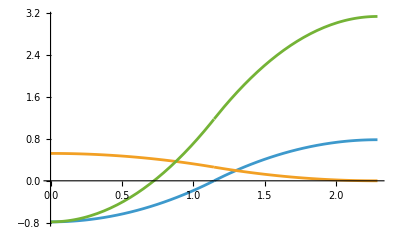

```mathematica
Plot[{q1Profile,q2Profile,q3Profile},{t,0,Tf}]
```

### 4) Assuming that the gravity force is negligible, m1 = 30 kg, m2 = 20 kg, m3 = 10 kg and that the links can be considered as lumped masses as shown in the picture (G1 and G2 at half the length of each link), find the equations of motion (do not report them). • Write the symbolic matrices J11, J22 and J33. • Plot the torque time profiles at joint 1 and 2 producing the motion found at point 3. Comment on the torque at joint 3. • Calculate the torque values at t = 0.5 s, 1 s, 1.5 s, 2 s .

```mathematica
massData={m1->30,m2->20,m3->10};
```

```mathematica
W01=Simplify[D[M01,t].Inverse[M01]];
W02=Simplify[D[M02,t].Inverse[M02]];
W03=Simplify[D[M03,t].Inverse[M03]];
```

```mathematica
J11={{0,0,0,0},{0,m1(-L1/2)^2,0,m1(-L1/2)},{0,0,0,0},{0,m2(-L1/2),0,m1}};
J11//MatrixForm
```

(0 | 0 | 0 | 0
0 | (L1^2 m1)/4 | 0 | -(L1 m1)/2
0 | 0 | 0 | 0
0 | -(L1 m2)/2 | 0 | m1)

```mathematica
J22={{m2(-L2/2)^2,0,m2(-L2/2)(-L3),m2(-L2/2)},{0,0,0,0},{m2(-L3)(-L2/2),0,m2(-L3)^2,m2(-L3)},{m2(-L2/2),0,m2(-L3),m2}};
J22//MatrixForm
```

((L2^2 m2)/4 | 0 | (L2 L3 m2)/2 | -(L2 m2)/2
0 | 0 | 0 | 0
(L2 L3 m2)/2 | 0 | L3^2 m2 | -L3 m2
-(L2 m2)/2 | 0 | -L3 m2 | m2)

```mathematica
J33={{m3(-L4)^2,0,0,m3(-L4)},{0,0,0,0},{0,0,0,0},{m3(-L4),0,0,m3}};
J33//MatrixForm
```

(L4^2 m3 | 0 | 0 | -L4 m3
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-L4 m3 | 0 | 0 | m3)

```mathematica
J10=Simplify[M01.J11.Transpose[M01]];
J20=Simplify[M02.J22.Transpose[M02]];
J30=Simplify[M03.J33.Transpose[M03]];
```

```mathematica
T1=Simplify[1/2 Tr[W01.J10.Transpose[W01]]]
```

0

```mathematica
T2=Simplify[1/2 Tr[W02.J20.Transpose[W02]]]
```

1/8 L2^2 m2 (Cos[q2[t]]^2 q1'[t]^2+q2'[t]^2)

```mathematica
T3=Simplify[1/2 Tr[W03.J30.Transpose[W03]]]
```

1/4 m3 ((L2^2+2 (L3+L5)^2+L2^2 Cos[2 q2[t]]) q1'[t]^2-4 L2 (L3+L5) Sin[q2[t]] q1'[t] q2'[t]+2 L2^2 q2'[t]^2)

Lagrangian term.

```mathematica
Lagr=FullSimplify[T1+T2+T3]
```

1/8 ((L2^2 m2 Cos[q2[t]]^2+2 m3 (L2^2+2 (L3+L5)^2+L2^2 Cos[2 q2[t]])) q1'[t]^2-8 L2 (L3+L5) m3 Sin[q2[t]] q1'[t] q2'[t]+L2^2 (m2+4 m3) q2'[t]^2)

Equation 1:

```mathematica
dLagrdq1dotdt=Simplify[D[D[Lagr,q1'[t]],t]]
```

1/8 (-2 L2^2 (m2+4 m3) Sin[2 q2[t]] q1'[t] q2'[t]-8 L2 (L3+L5) m3 Cos[q2[t]] q2'[t]^2+2 (L2^2 m2 Cos[q2[t]]^2+2 m3 (L2^2+2 (L3+L5)^2+L2^2 Cos[2 q2[t]])) q1''[t]-8 L2 (L3+L5) m3 Sin[q2[t]] q2''[t])

```mathematica
dLagrdq1=Simplify[D[Lagr,q1[t]]]
```

0

Equation 2:

```mathematica
dLagrdq2dotdt=Simplify[D[D[Lagr,q2'[t]],t]]
```

1/4 L2 (-4 (L3+L5) m3 Cos[q2[t]] q1'[t] q2'[t]-4 (L3+L5) m3 Sin[q2[t]] q1''[t]+L2 (m2+4 m3) q2''[t])

```mathematica
dLagrdq2=Simplify[D[Lagr,q2[t]]]
```

-1/4 L2 Cos[q2[t]] q1'[t] (L2 (m2+4 m3) Sin[q2[t]] q1'[t]+4 (L3+L5) m3 q2'[t])

Equation 3 :

```mathematica
dLagrdq3dotdt=Simplify[D[D[Lagr,q3'[t]],t]]
```

0

```mathematica
dLagrdq3=Simplify[D[Lagr,q3[t]]]
```

0

Equation of Motion

```mathematica
equation1=dLagrdq1dotdt-dLagrdq1-C1//Simplify
```

1/8 (-8 C1-2 L2^2 (m2+4 m3) Sin[2 q2[t]] q1'[t] q2'[t]-8 L2 (L3+L5) m3 Cos[q2[t]] q2'[t]^2+2 (L2^2 m2 Cos[q2[t]]^2+2 m3 (L2^2+2 (L3+L5)^2+L2^2 Cos[2 q2[t]])) q1''[t]-8 L2 (L3+L5) m3 Sin[q2[t]] q2''[t])

```mathematica
equation2=dLagrdq2dotdt-dLagrdq2-C2//Simplify
```

1/8 (-8 C2+L2^2 (m2+4 m3) Sin[2 q2[t]] q1'[t]^2-8 L2 (L3+L5) m3 Sin[q2[t]] q1''[t]+2 L2^2 m2 q2''[t]+8 L2^2 m3 q2''[t])

```mathematica
equation3=dLagrdq3dotdt-dLagrdq3-C3//Simplify
```

-C3

We obtained  always. Therefore, joint 3 can move without consuming energy. This happened because the Lagrangian term does not depend on  nor , then the derivative is null.
This behavior occurred because we are using lumped parameters and  is located in  which is located on the axis . Then, by moving  we do mot move the mass . Since a point mass has zero rotational inertia, rotating it about its own center does not generate kinetic energy nor require torque.

Inverse Dynamic

```mathematica
C1InvDyn=C1/.Flatten[Solve[equation1==0,C1]]
```

1/4 (-L2^2 m2 Sin[2 q2[t]] q1'[t] q2'[t]-4 L2^2 m3 Sin[2 q2[t]] q1'[t] q2'[t]-4 L2 L3 m3 Cos[q2[t]] q2'[t]^2-4 L2 L5 m3 Cos[q2[t]] q2'[t]^2+2 L2^2 m3 q1''[t]+4 L3^2 m3 q1''[t]+8 L3 L5 m3 q1''[t]+4 L5^2 m3 q1''[t]+L2^2 m2 Cos[q2[t]]^2 q1''[t]+2 L2^2 m3 Cos[2 q2[t]] q1''[t]-4 L2 L3 m3 Sin[q2[t]] q2''[t]-4 L2 L5 m3 Sin[q2[t]] q2''[t])

```mathematica
C2InvDyn=C2/.Flatten[Solve[equation2==0,C2]]
```

1/8 (L2^2 m2 Sin[2 q2[t]] q1'[t]^2+4 L2^2 m3 Sin[2 q2[t]] q1'[t]^2-8 L2 L3 m3 Sin[q2[t]] q1''[t]-8 L2 L5 m3 Sin[q2[t]] q1''[t]+2 L2^2 m2 q2''[t]+8 L2^2 m3 q2''[t])

```mathematica
C3InvDyn=C3/.Flatten[Solve[equation3==0,C3]]
```

0

Plot Torques Profiles

```mathematica
C1InvDynNum=C1InvDyn/.lenData/.massData/.q1[t]->q1Profile/.q1'[t]->D[q1Profile,t]/.q1''[t]->D[q1Profile,t,t]/.q2[t]->q2Profile/.q2'[t]->D[q2Profile,t]/.q2''[t]->D[q2Profile,t,t]/.q3[t]->q3Profile/.q3'[t]->D[q3Profile,t]/.q3''[t]->D[q3Profile,t,t]
```

1/4 (15. (Piecewise[{{0, t<0}, {1.2, 0<t<116753425/102047017}, {-1.2, 116753425/102047017<t<123896947/54145366}, {0, t>123896947/54145366}, {Indeterminate, True}}])+5. Cos[Piecewise[{{π/6-0.2 t^2, 0≤t≤1.14411}, {0.+0.2 (2.28823-t)^2, 1.14411<t≤2.28823}, {0, True}}]]^2 (Piecewise[{{0, t<0}, {1.2, 0<t<116753425/102047017}, {-1.2, 116753425/102047017<t<123896947/54145366}, {0, t>123896947/54145366}, {Indeterminate, True}}])+5. Cos[2 (Piecewise[{{π/6-0.2 t^2, 0≤t≤1.14411}, {0.+0.2 (2.28823-t)^2, 1.14411<t≤2.28823}, {0, True}}])] (Piecewise[{{0, t<0}, {1.2, 0<t<116753425/102047017}, {-1.2, 116753425/102047017<t<123896947/54145366}, {0, t>123896947/54145366}, {Indeterminate, True}}])-10. Cos[Piecewise[{{π/6-0.2 t^2, 0≤t≤1.14411}, {0.+0.2 (2.28823-t)^2, 1.14411<t≤2.28823}, {0, True}}]] (Piecewise[{{0, t<0}, {-0.4 t, 0<t<116753425/102047017}, {0.4 (-2.28823+t), 116753425/102047017<t<123896947/54145366}, {0., t==123896947/54145366}, {0, t>123896947/54145366}, {Indeterminate, True}}])^2-10. (Piecewise[{{0, t<0}, {-0.4, 0<t<116753425/102047017}, {0.4, 116753425/102047017<t<123896947/54145366}, {0, t>123896947/54145366}, {Indeterminate, True}}]) Sin[Piecewise[{{π/6-0.2 t^2, 0≤t≤1.14411}, {0.+0.2 (2.28823-t)^2, 1.14411<t≤2.28823}, {0, True}}]]-15. (Piecewise[{{0, t<0}, {1.2 t, 0<t<116753425/102047017}, {-0.6 (-4.57646+2 t), 116753425/102047017<t<123896947/54145366}, {0, t>123896947/54145366}, {Indeterminate, True}}]) (Piecewise[{{0, t<0}, {-0.4 t, 0<t<116753425/102047017}, {0.4 (-2.28823+t), 116753425/102047017<t<123896947/54145366}, {0., t==123896947/54145366}, {0, t>123896947/54145366}, {Indeterminate, True}}]) Sin[2 (Piecewise[{{π/6-0.2 t^2, 0≤t≤1.14411}, {0.+0.2 (2.28823-t)^2, 1.14411<t≤2.28823}, {0, True}}])])

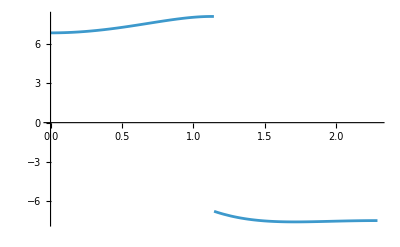

```mathematica
Plot[C1InvDynNum,{t,0,Tf}]
```

```mathematica
C2InvDynNum=C2InvDyn/.lenData/.massData/.q1[t]->q1Profile/.q1'[t]->D[q1Profile,t]/.q1''[t]->D[q1Profile,t,t]/.q2[t]->q2Profile/.q2'[t]->D[q2Profile,t]/.q2''[t]->D[q2Profile,t,t]/.q3[t]->q3Profile/.q3'[t]->D[q3Profile,t]/.q3''[t]->D[q3Profile,t,t]
```

1/8 (30. (Piecewise[{{0, t<0}, {-0.4, 0<t<116753425/102047017}, {0.4, 116753425/102047017<t<123896947/54145366}, {0, t>123896947/54145366}, {Indeterminate, True}}])-20. (Piecewise[{{0, t<0}, {1.2, 0<t<116753425/102047017}, {-1.2, 116753425/102047017<t<123896947/54145366}, {0, t>123896947/54145366}, {Indeterminate, True}}]) Sin[Piecewise[{{π/6-0.2 t^2, 0≤t≤1.14411}, {0.+0.2 (2.28823-t)^2, 1.14411<t≤2.28823}, {0, True}}]]+15. (Piecewise[{{0, t<0}, {1.2 t, 0<t<116753425/102047017}, {-0.6 (-4.57646+2 t), 116753425/102047017<t<123896947/54145366}, {0, t>123896947/54145366}, {Indeterminate, True}}])^2 Sin[2 (Piecewise[{{π/6-0.2 t^2, 0≤t≤1.14411}, {0.+0.2 (2.28823-t)^2, 1.14411<t≤2.28823}, {0, True}}])])

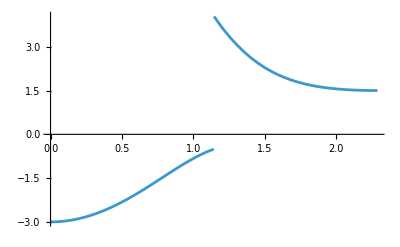

```mathematica
Plot[C2InvDynNum,{t,0,Tf}]
```

```mathematica
C3InvDynNum=C3InvDyn/.lenData/.massData/.q1[t]->q1Profile/.q1'[t]->D[q1Profile,t]/.q1''[t]->D[q1Profile,t,t]/.q2[t]->q2Profile/.q2'[t]->D[q2Profile,t]/.q2''[t]->D[q2Profile,t,t]/.q3[t]->q3Profile/.q3'[t]->D[q3Profile,t]/.q3''[t]->D[q3Profile,t,t]
```

0

Torque Values at Custom t

```mathematica
C1InvDynNum/.t->0.5
```

7.29631

```mathematica
C2InvDynNum/.t->0.5
```

-2.32032

```mathematica
C1InvDynNum/.t->1
```

8.06905

```mathematica
C2InvDynNum/.t->1
```

-0.825969

```mathematica
C1InvDynNum/.t->1.5
```

-7.52634

```mathematica
C2InvDynNum/.t->1.5
```

2.28444

```mathematica
C1InvDynNum/.t->2
```

-7.54363

```mathematica
C2InvDynNum/.t->2
```

1.5573